```mathematica
Ln1=4;
Ln2=1;
c=2;
```

P(l1<L1, l2< L2)

```mathematica
P1[l1_,l2_,c_,γ_]:=((l1+l2+c-1)!)/((c-1)!l1!l2!)*(1/(2+γ))^(l1+l2)(γ/(2+γ))^c
```

P(l1<L1,l2=L2)

```mathematica
P2[l1_,L2_,c_,γ_]:=((l1+c-1)!)/(l1!(c-1)!)*γ^c/(γ+1)^(l1+c)-Sum[((l1+l2+c-1)!)/((c-1)!l1!l2!)*γ^c/(γ+2)^(l1+l2+c),{l2,0,L2-1}]
```

P(l1=L1,l2=L2). First term is all structures l1=(0-L1-1), l2=(0:L2). Second term is l1=L1, l2=L2-1. Note that L1 cannot be less than 1.

```mathematica
P3[L1_,L2_,c_,γ_]:=1-Sum[Sum[P1[l1,l2,c,γ],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ],{l2,0,L2-1}]
```

Note that also L2 Cannot be less than 1.

Entropy

```mathematica
En[L1_,L2_,c_,γ_]:=-Sum[Sum[P1[l1,l2,c,γ]*Log[P1[l1,l2,c,γ]],{l1,0,L1-1}],{l2,0,L2-1}]-Sum[P2[l1,L2,c,γ]*Log[P2[l1,L2,c,γ]],{l1,0,L1-1}]-Sum[P2[l2,L1,c,γ]*Log[P2[l2,L1,c,γ]],{l2,0,L2-1}]-P3[L1,L2,c,γ]*Log[P3[L1,L2,c,γ]]
```

For comparison P(l<L, c=1)

```mathematica
P11[l_,p_]:=(1-p)* p^l
```

P(l=L,c=1)

```mathematica
P21[L_,p_]:=p^L
```

Entropy c=1

```mathematica
EN[L_,p_]:=-(Sum[P11[l,p]*Log[P11[l,p]],{l,0,L-1}]+p^L*Log[p^L])
```

```mathematica
h[τ_]:=1/(1+1/τ)
```

Relative Entropies!

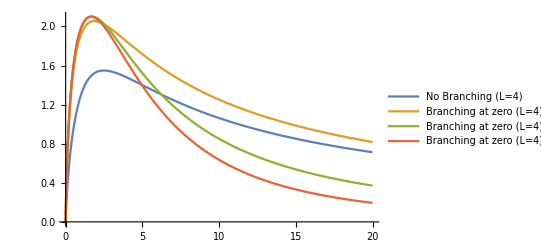

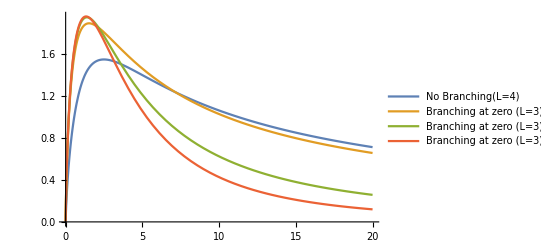

```mathematica
Plot[{EN[4,h[τ]],En[4,1,1,1/τ], En[4,1,2,2/τ],En[4,1,3,3/τ]},{τ,0,20},PlotLegends->{"No Branching (L=4)","Branching at zero (L=4) c=1","Branching at zero (L=4) c=2","Branching at zero (L=4) c=3"}]
Plot[{EN[4,h[τ]],En[3,1,1,1/τ], En[3,1,2,2/τ],En[3,1,3,3/τ]},{τ,0,20},PlotLegends->{"No Branching(L=4) ","Branching at zero (L=3) c=1","Branching at zero (L=3) c=2","Branching at zero (L=3) c=3"}]
```

Yields of Each Species, especially comparing Terminating Structures

```mathematica
T1=Evaluate@Table[P1[l1,l2,c,c/τ], {l1,0,Ln1-1},{l2,0,Ln2-1}]; 
T2=Evaluate@Table[P2[l1,Ln2,c,c/τ],{l1,0,Ln1-1}];
T3=Evaluate@Table[P2[l1,Ln1,c,c/τ],{l1,0,Ln2-1}];
```

Yields of Each Species Out of P=1 total

```mathematica
NT1=Length[T1];
NT2=Length[T2]
NT3=Length[T3];

T12=Evaluate@Table[Sum[T1[[{i}]],{i,1,j}],{j,1,NT1}];
T22=Evaluate@Table[T12[[NT1]]+Sum[T2[[{i}]],{i,1,j}],{j,1,NT2}];
T32=Evaluate@Table[T22[[NT2]]+Sum[T3[[{i}]],{i,1,j}],{j,1,NT3}];
CU1[L1_,L2_,c_,γ_]:=T32[[NT3]]+P3[L1,L2,c,γ];
```

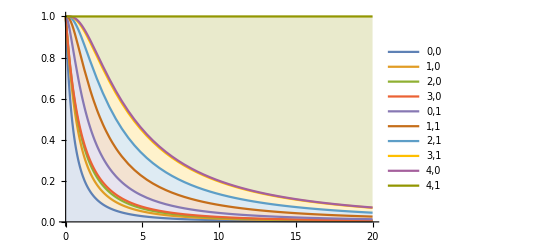

```mathematica
Plot[{T12,T22,T32,CU1[Ln1,Ln2,c,c/τ]},{τ,0,20},Filling->{1->Axis,2->{1},3->{2},4->{3},5->{4},6->{5},7->{6},8->{7},9->{8},10->{9}},PlotLegends->{"0,0","1,0","2,0","3,0","0,1","1,1","2,1","3,1","4,0","4,1"}]
```